```mathematica
a=Import["ExampleData/coneflower.jpg","Data"];
```

```mathematica
a=Import["ExampleData/spikey3.bmp","Data"];
b=Import["ExampleData/spikey3.bmp"];
dim=Dimensions[a]
```

{108,120,3}

```mathematica
nx=dim⟦1⟧;
ny=dim⟦2⟧;
xmax = 2.;
xmin=-2.;
ymax=2.;
ymin=-2.;
t1[x_]:={(x⟦1⟧-1)/(nx-1)(xmax-xmin)+xmin,(x⟦2⟧-1)/(ny-1)(ymax-ymin)+ymin}
g[x_]:={x⟦1⟧/(x⟦1⟧^2+x⟦2⟧^2),x⟦2⟧/(x⟦1⟧^2+x⟦2⟧^2)}
```

```mathematica
t=Flatten[Table[If[Norm[t1[{n1,n2}]]>0.4,{RGBColor[a⟦n1,n2⟧⟦1⟧/256.,a⟦n1,n2⟧⟦2⟧/256.,a⟦n1,n2⟧⟦3⟧/256.],Polygon[{g[t1[{n1,n2}]],g[t1[{n1,n2+1}]],g[t1[{n1+1,n2+1}]],g[t1[{n1+1,n2}]]}]},{}],{n1,1,nx},{n2,1,ny}]];
```

```mathematica
g1=Graphics[t];
```

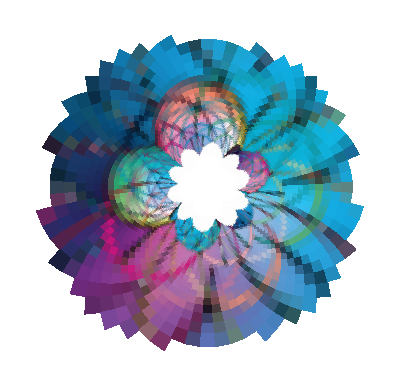

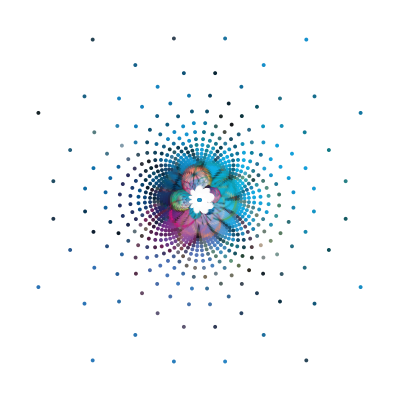

```mathematica
GraphicsRow[{g1,b}]
```